```mathematica
f[n_]:=(1/(n+1)∑_(k=0)^n Binomial[n,k])^(1/n)
```

```mathematica
N[Limit[f[n],n->Infinite]]
```

(2.^Infinite/Infinite)^(1/Infinite)

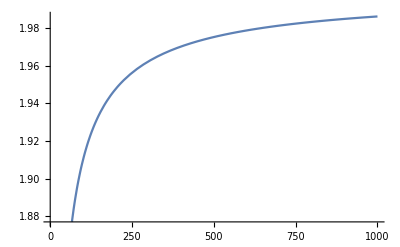

```mathematica
Plot[f[x],{ x,1,1000}]
```

```mathematica
g[n_]:=((∏_(k=0)^n Binomial[n,k])^(1/(n+1)))^(1/n)
```

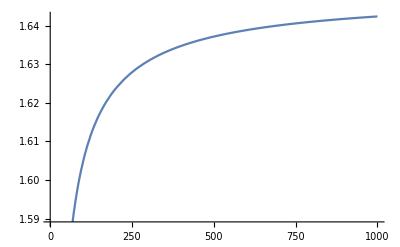

```mathematica
Plot[g[x],{ x,1,1000}]
```

```mathematica
N[Sqrt[E]]
```

1.64872